```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/data_v2/small_stepsize_T

```mathematica
dataall=Table[Import["../Shi_small_stepsizeT_v2/Shi_mu="<>ToString[i]<>"_m0=600-flag_4-51x1031_VC=true.csv"][[2;;1032]],{i,800,960,1}];
```

```mathematica
n=Length[Table[i,{i,800,960,1}]]
```

161

```mathematica
m=Length[Table[i,{i,17,70,0.1}]]
```

531

```mathematica
dataall[[1]][[1]]
```

{0.000245755,0.00024603,0.000246578,0.000247401,0.000248497,0.000249866,0.000251507,0.000253419,0.000255601,0.000258052,0.000260768,0.000263748,0.000266988,0.000270485,0.000274233,0.000278228,0.000282464,0.000286933,0.000291626,0.000296534,0.000301647,0.000306952,0.000312435,0.000318082,0.000323875,0.000329796,0.000335826,0.000341942,0.000348122,0.000354341,0.000360574,0.000366791,0.000372966,0.000379067,0.000385065,0.000390929,0.000396625,0.000402123,0.000407391,0.000412397,0.000417111,0.000421503,0.000425545,0.000429211,0.000432475,0.000435317,0.000437716,0.000439656,0.000441123,0.000442107,0.000442601}

```mathematica
pdata=Table[ParallelTable[Export["./mub"<>ToString[(i-1)+800]<>"/V"<>ToString[j]<>".dat",Table[dataall[[i]][[k]][[j]],{k,1,531}]],{j,1,51}],{i,1,161}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[800+(i-1)*1]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,161}],{j,1,51}];
```

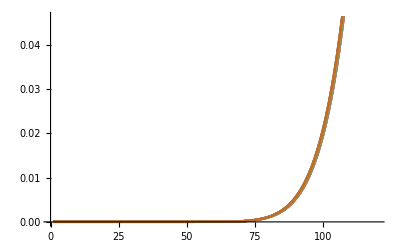

```mathematica
ListLinePlot[pdata[[1]]]
```